# S - gaussian smearing

## sharp trap switch, g smear, go futher with the transition probability

## set some parameters

```mathematica
α=1;
```

```mathematica
numSteps=200;
```

```mathematica
σMin=0.1;  σMax=2;  σStepSize=Abs[σMin-σMax]/numSteps;
σValues=Table[σ,{σ,σMin,σMax,σStepSize}];
```

```mathematica
clear[λ]
```

clear[0.1]

## the smearing function

```mathematica
fG[x_,σ_]:=1/(σ*√π)ⅇ^(-x^2/σ^2)
ftilG[k_,σ_]:=FourierTransform[fG[x,σ],x,k,FourierParameters->{1,-1},Assumptions->σ∈Reals&&σ>0]
```

### the k integrand

```mathematica
ggintegrandgd[k_,σ_]:=A^4/(2 π r^2) ⅇ^(-k ε) k ftilG[k,σ]^2 (-(2 Sin[c (-k+Ω)]^2)/(-k+Ω)^2-(2 Sin[c (k+Ω)]^2)/(k+Ω)^2)
```

## the transition probability, numerically, starting in the ground state

use numerical integration; still want to plot as a function of σ, so we’ll have to use Table, or ParallelTable for using the cluster

```mathematica
c=1;r=0.2;Ω=1;A=1/(r+2*c);
```

### with an ε regularized cutoff (exp)

```mathematica
ε=0.2;
```

```mathematica
pexpG=Table[α+λ^2*NIntegrate[ggintegrandgd[k,σ],{k,0,∞}],{σ,σMin,σMax,σStepSize}];
```

### with no cutoff (ε:=0)

```mathematica
ε=0;
```

```mathematica
pnoneG=Table[α+λ^2*NIntegrate[ggintegrandgd[k,σ],{k,0,∞}],{σ,σMin,σMax,σStepSize}];
```

### with a sharp cutoff (ε:=0 and integrate only up to a constant)

```mathematica
ε=0;   cutoff=5*Ω;
```

```mathematica
psharpG=Table[α+λ^2*NIntegrate[ggintegrandgd[k,σ],{k,0,cutoff}],{σ,σMin,σMax,σStepSize}];
```

#### with a different cutoff (later) (ε:=0 and cutoff[k_]:=something)

## plot p v σ

```mathematica
λ=0.1;
```

#### put the data into lists for plotting

```mathematica
dataExpCutoffG     =Transpose[{σValues,pexpG}];
dataNoCutoffG       =Transpose[{σValues,pnoneG}];
dataSharpCutoffG=Transpose[{σValues,psharpG}];
```

### ploot

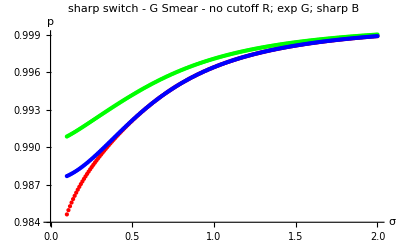

```mathematica
ListPlot[{dataNoCutoffG,dataExpCutoffG,dataSharpCutoffG},
AxesLabel->{σ,p},
PlotStyle->{Red,Green,Blue,Black},
PlotLabel->Style["sharp switch - G Smear - no cutoff R; exp G; sharp B",FontSize->16]]
```

## status